#### Illustrate a problematic elastic map for the built-in Mathematica function NMinimize INSTRUCTIONS: Run common_funs.nb, ES_FindSymGroups.nb, chooseTmat.nb, then this notebook

```mathematica
Tmat = TmatBrown;
```

#### The problematic point is between TET and XISO (dt =0.2):

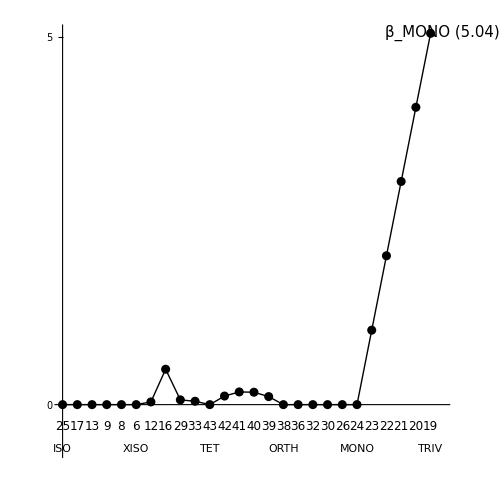

#### Define a function to minimize a square patch. Adjust dθ based on how close the local minima are.

```mathematica
dtheta = 0.2π; dphi=dtheta;
```

```mathematica
Flocal[theta0_,phi0_,
ta_,dphi_,Tmat_]:=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],theta0-dtheta≤θ≤theta0+dtheta&&phi0-dphi≤ϕ≤phi0+dphi},{θ,ϕ},Method->"RandomSearch"]
```

#### GetTempAndθ0σ0ϕ0 from ES_FindSymGroups.nb (θ search range to 2π)

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤2π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
```

#### Check the starting value of TRIV (beta = 5.04)

```mathematica
WantDetails="WantDetails";
OutputFor[Tmat,MONO]
```

#### Get the closest TET and XISO

```mathematica
OutputFor[Tmat,TET]
OutputFor[Tmat,XISO]
```

#### Reconstruct the problematic map. For the dt = 0.2 lattice, this is a point between 43 (TET) and 6 (XISO): 43 (TET), 33, 29, 16*, 12, 6 (XISO)

```mathematica
TmatTET=Closest[Tmat,TET];
TmatXISO=Closest[Tmat,XISO];
Tmatx=0.4TmatTET+0.6TmatXISO;
MatrixForm[TmatTET]
MatrixForm[TmatXISO]
MatrixForm[Tmatx]
```

#### This fails to find the global minimum:

```mathematica
OutputFor[Tmatx,MONO]
```

```mathematica
βT[Tmatx,MONO]/Degree
```

#### CORRECT MINIMUM: blue patch near θ = 0

```mathematica
Flocal[π,0.5π,dtheta,dphi,Tmatx]
Flocal[0,0.5π,dtheta,dphi,Tmatx]
```

#### INCORRECT MINIMUM: blue path near θ = pi/2

```mathematica
Flocal[0.5π,0.5π,dtheta,dphi,Tmatx]
Flocal[1.5π,0.5π,dtheta,dphi,Tmatx]
```

#### LOCAL MINIMUM: blue patch near poles

```mathematica
Flocal[0.7π,0.9π,dtheta,dphi,Tmatx]
Flocal[1.7π,0.1π,dtheta,dphi,Tmatx]
```

#### Change the θ search range to π, and then it finds the global minimum:

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
```

```mathematica
OutputFor[Tmatx,MONO]
```

```mathematica
βT[Tmatx,MONO]/Degree
```